#### Import Iris Data

```mathematica
url="https://raw.githubusercontent.com/jbrownlee/Datasets/master/iris.csv";
dataset=Import[url];
(*names={'sepal-length','sepal-width','petal-length','petal-width','class'}*)
Dimensions[dataset]
dataset[[1;;5]]
dataset[[All,5]]//Tally
```

{150,5}

{{5.1,3.5,1.4,0.2,Iris-setosa},{4.9,3.,1.4,0.2,Iris-setosa},{4.7,3.2,1.3,0.2,Iris-setosa},{4.6,3.1,1.5,0.2,Iris-setosa},{5.,3.6,1.4,0.2,Iris-setosa}}

{{Iris-setosa,50},{Iris-versicolor,50},{Iris-virginica,50}}

#### Iris Data Subset

```mathematica
sepalLength=dataset[[All,1]];
petalLength=dataset[[All,3]];
petalWidth=dataset[[All,4]];
sepalWidth=dataset[[All,2]];
class=dataset[[All,5]]/.{"Iris-setosa"->"setosa", "Iris-versicolor"->"versicolor", "Iris-virginica"->"virginica"};
```

#### Split data into training and validation for classification

```mathematica
geomdata=Thread[{sepalLength,sepalWidth,petalLength,petalWidth}];
mldata=RandomSample[Thread[geomdata->class]];
s=Dimensions[mldata][[1]]
training=mldata[[1;;120]];
validation=mldata[[120;;150]];
```

150

#### Classification

```mathematica
ciris=Classify[training,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

#### Classifier measurements

```mathematica
cm=ClassifierMeasurements[ciris,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

1.

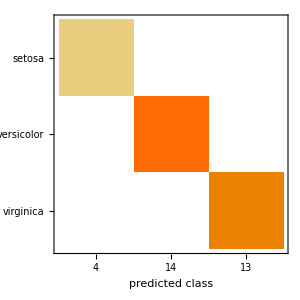

```mathematica
cm["ConfusionMatrixPlot"]
```

#### Misc

```mathematica
subset1=Thread[{sepalWidth,petalWidth}];
c1=FindClusters[subset1,Method->"Spectral"];

subset2=Thread[{sepalLength,sepalWidth}];
c2=FindClusters[subset2,Method->"Spectral"];

subset3=Thread[{petalLength,petalWidth}];
c3=FindClusters[subset3,Method->"Spectral"];

subset4=Thread[{petalLength,class}];
c4=FindClusters[subset4];
```

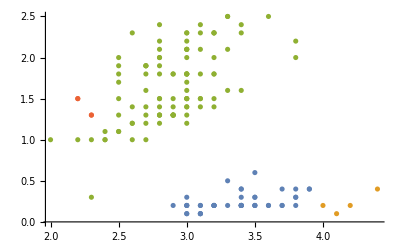
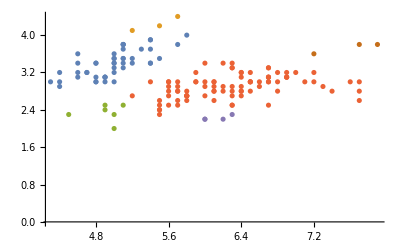
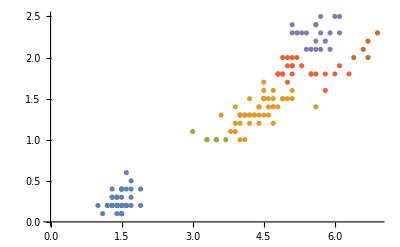
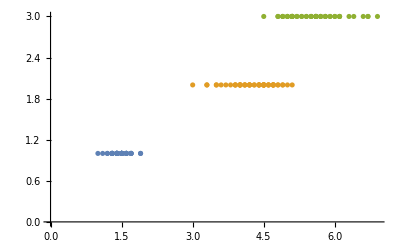

```mathematica
{ListPlot[c1],ListPlot[c2],ListPlot[c3],ListPlot[c4]}
```

```mathematica
geomdata=Thread[{sepalLength,sepalWidth,petalLength,petalWidth}];
mldata=RandomSample[Thread[geomdata->class]];
```

```mathematica
s=Dimensions[mldata][[1]]
training=mldata[[1;;90]];
validation=mldata[[90;;150]];
p=Predict[training,Method->"GradientBoostedTrees"]
```

150

PredictorFunction[…]

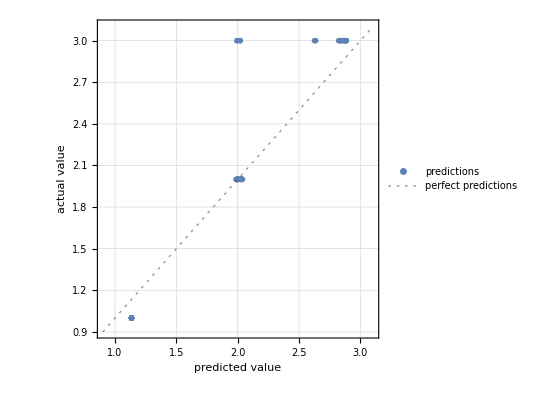

0.280655

```mathematica
pm1=PredictorMeasurements[p,validation];
pm1["ComparisonPlot"]
PredictorMeasurements[p,validation, "StandardDeviation"]
```

```mathematica
cf=Classify[mldata,Method->"DecisionTree"];
```

```mathematica
cf
```

ClassifierFunction[…]